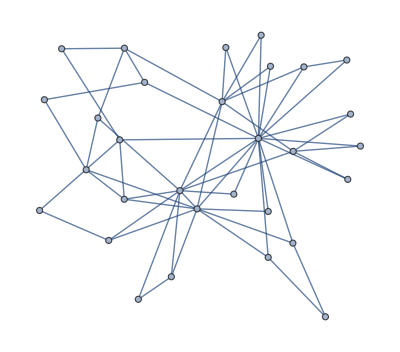

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[30,2]]
```

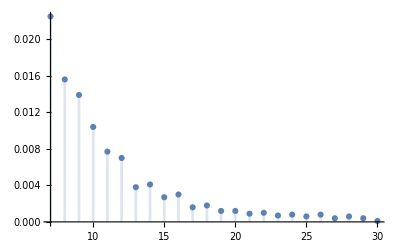

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[10^4,2]];
EmpiricalDistribution[VertexDegree[%]];
DiscretePlot[PDF[%,k],{k,7,30}]
```

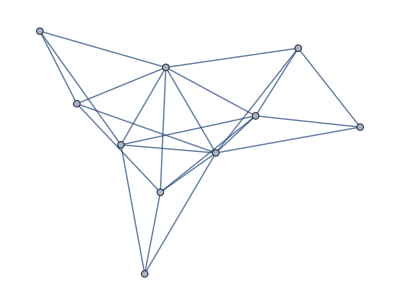

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[10,3]]
```

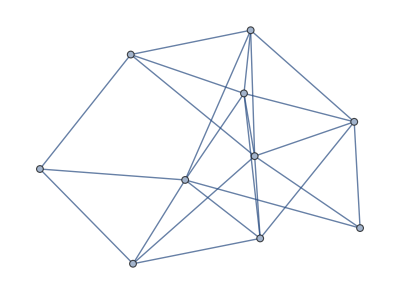
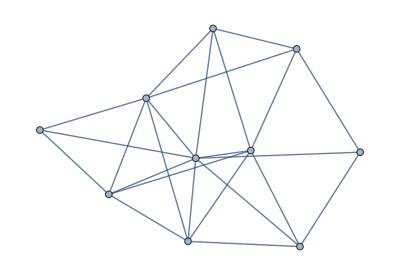
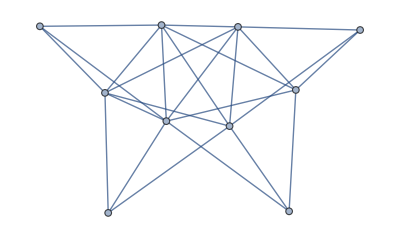
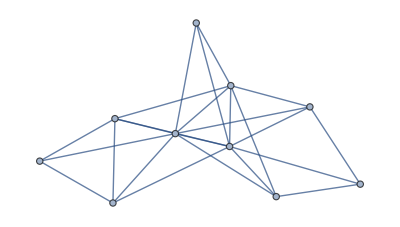

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[10,3],4]
```

```mathematica
𝒟=GraphPropertyDistribution[VertexDegree[g,1],g\[Distributed]BarabasiAlbertGraphDistribution[30,4]];
```

```mathematica
NProbability[x>=10,x\[Distributed]𝒟]
```

0.881682

```mathematica
g=ExampleData[{"NetworkGraph","Internet"}];
```

```mathematica
𝒢=BarabasiAlbertGraphDistribution[VertexCount[g],Round[EdgeCount[g]/VertexCount[g]]]
```

BarabasiAlbertGraphDistribution[22963,2]

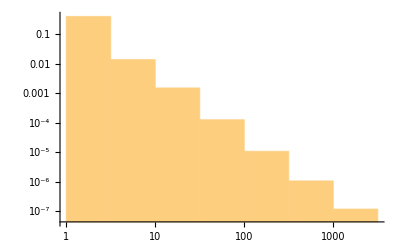
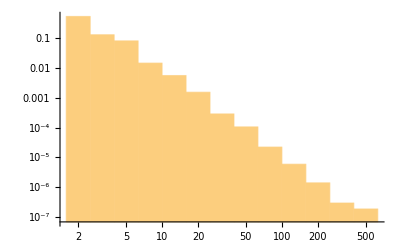

```mathematica
{Histogram[VertexDegree[g],{"Log",10},{"Log","PDF"}],Histogram[VertexDegree[RandomGraph[𝒢]],{"Log",10},{"Log","PDF"}]}
```

```mathematica
N[GlobalClusteringCoefficient[RandomGraph[𝒢]]]
```

0.000783674

```mathematica
N[GlobalClusteringCoefficient[g]]
```

0.0111464

```mathematica
g=ExampleData[{"NetworkGraph","PowerGrid"}];
```

```mathematica
𝒢=BarabasiAlbertGraphDistribution[VertexCount[g],Round[EdgeCount[g]/VertexCount[g]]]
```

BarabasiAlbertGraphDistribution[4941,1]

```mathematica
f[g_]:=Map[{#[[1]],#[[2]]/VertexCount[g]}&,Tally[VertexDegree[g]]];
```

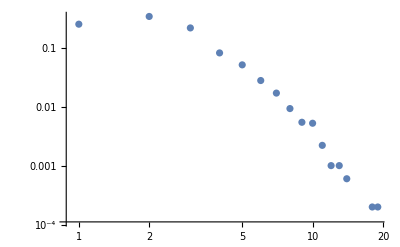
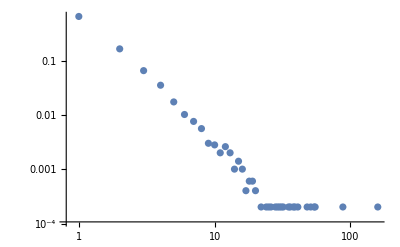

```mathematica
{ListLogLogPlot[f[g]],ListLogLogPlot[f[RandomGraph[𝒢]]]}
```

```mathematica
𝒟=GraphPropertyDistribution[VertexEccentricity[g,First[GraphHub[g]]],g\[Distributed]BarabasiAlbertGraphDistribution[400,3]];
```

```mathematica
NExpectation[x,x\[Distributed]𝒟]
```

3.298

```mathematica
GraphPropertyDistribution[VertexCount[g],g\[Distributed]BarabasiAlbertGraphDistribution[n,k]]
```

DiscreteUniformDistribution[{n,n}]

```mathematica
GraphPropertyDistribution[EdgeCount[g],g\[Distributed]BarabasiAlbertGraphDistribution[n,k]]
```

DiscreteUniformDistribution[{1/2 k (-1-k+2 n),1/2 k (-1-k+2 n)}]

```mathematica
𝒟[n_,k_]:=EmpiricalDistribution[VertexDegree[RandomGraph[BarabasiAlbertGraphDistribution[n,k]]]];
```

SetDelayed::write: Tag GraphPropertyDistribution in GraphPropertyDistribution[VertexEccentricity[\[FormalG],First[GraphHub[\[FormalG]]]],\[FormalG]\[Distributed]BarabasiAlbertGraphDistribution[400,3]][n_,k_] is Protected.

```mathematica
ℰ=TruncatedDistribution[{5,∞},ZipfDistribution[2]];
```

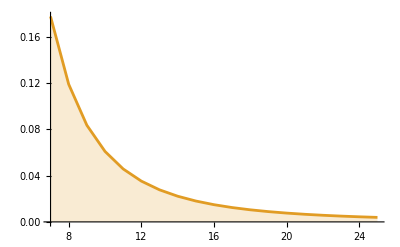

```mathematica
DiscretePlot[Evaluate[{PDF[𝒟[10^4,6],d],PDF[ℰ,d]}],{d,7,25},Joined->True]
```

```mathematica
PDF[ℰ,d]
```

Piecewise[{{1/(d^3 (1-256103/(216000 Zeta[3])) Zeta[3]), d>5}, {0, True}}]

```mathematica
barabasi[n_,k_]/;n<=k+1:=CompleteGraph[n]
```

```mathematica
barabasi[n_,k_]/;n>k+1:=Module[{g=barabasi[n-1,k]},Graph[Join[EdgeList[g],Map[n<->#&,RandomSample[VertexDegree[g]->VertexList[g],k]]]]]
```

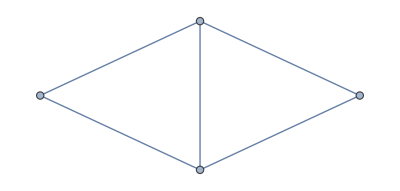
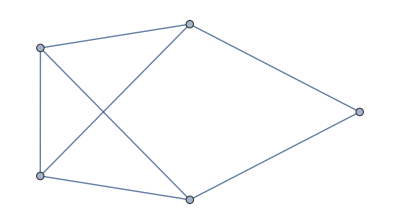
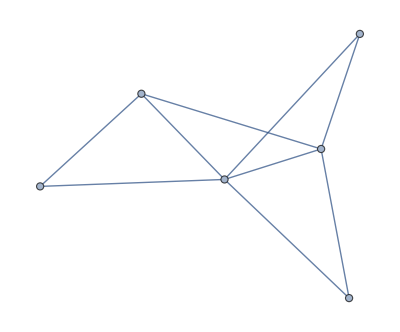
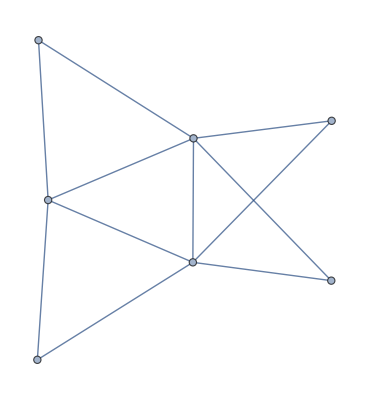

```mathematica
Table[barabasi[n,2],{n,4,7}]
```

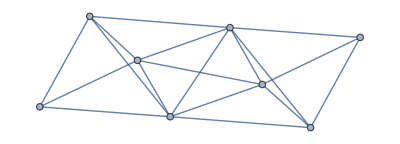

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[8,3]]
```

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[8,3]];
FindClique[%]
```

{{1,2,3,4}}

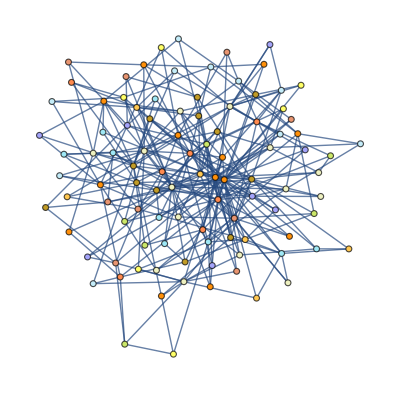

```mathematica
HighlightGraph[RandomGraph[BarabasiAlbertGraphDistribution[10^2,3]],Table[Style[i,RandomChoice[ColorData[45,"ColorList"]]],{i,10^2}]]
```